### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
{timedata,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 20,I2->200000, U1-> 200,U2->100,U3->0}];
timedata
{time,{system,rules}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

0.11061

3
0

1.97569

```mathematica
{time,rules}=AbsoluteTiming@Solver[d2e][alpha=1];
time
```

The error (1-Norm of LHS-RHS) is 3.63043×10^-14

The error is 3.63043×10^-14 which is less than 1.×10^-10

It took 6.46393 seconds to solve!
	The system is True

6.46547

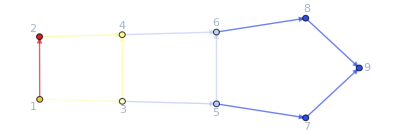

```mathematica
ColorNetworkByValueFunctionOperator[d2e][rules]
```

```mathematica
{timedata,d2e}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timedata;
{time,{system,result}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

1.4913

```mathematica
result=Solver[d2e][alpha=1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 5.54414 seconds to solve!
	The system is True

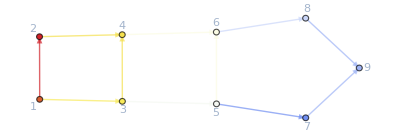

```mathematica
ColorNetworkByValueFunctionOperator[d2e][result]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

1.9647

```mathematica
{time,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

0.102996

2.26777

#### Non-linear case

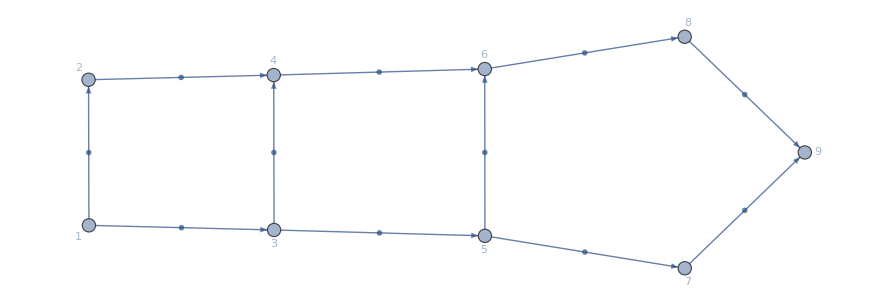

-Graphics-

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e;
FFR=rules;
BEL=EdgeList[MFGEquations["BG"]];
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@BEL;
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@BEL;
Graph[MFGEquations["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[MFGEquations["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Solver[d2e][alpha = .1]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[Values@d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]]
```

```mathematica
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
```

```mathematica
rules0=AssociationThread[Values @ d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

length of system: 238

number of alernatives: 80

length of system after eliminating us: 232

new number of alernatives: 76

CCS:
j1≥0&&j2≥0&&8/7+j29≥0&&6/7+j30≥0&&4/7+j31≥0&&4/7+j32≥0&&4/7+j31≥0&&6/7+j34≥0&&8/7+j35≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j16≥0&&j23≥0&&j24≥0&&-2+j1≥0&&-2+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j31≥0&&j34≥0&&j35≥0&&-6/7+j10≥0&&-6/7+j11≥0&&-4/7+j12≥0&&-6/7+j13≥0&&-8/7+j14≥0&&-4/7+j15≥0&&-4/7+j16≥0&&-6/7+j17≥0&&-4/7+j18≥0&&-6/7+j19≥0&&-6/7+j20≥0&&-2+j21≥0&&-4/7+j16≥0&&-8/7+j23≥0&&-2+j24≥0&&-2+j1≥0&&-2+j2≥0&&2+j1-j2≥0&&2-j1+j2≥0&&-6/7+j1-j30+jt10≥0&&6/7+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-2+j1-j29+jt10≥0&&2-j1+j29+j30-jt10≥0&&jt13≥0&&8/7+j29-jt13≥0&&4/7+j29+j31-j32-jt13≥0&&-4/7-j29+j32+jt13≥0&&-4/7-j31+j32+jt13≥0&&4/7+j31-jt13≥0&&4/7+j31≥0&&j31≥0&&jt21≥0&&j2-jt21≥0&&-8/7+j2+j34-j35-jt21≥0&&8/7-j2+j35+jt21≥0&&-6/7-j34+j35+jt21≥0&&6/7+j34-jt21≥0&&jt27≥0&&jt28≥0&&6/7+j30-jt27-jt28≥0&&jt30≥0&&jt31≥0&&6/7+j34-jt30-jt31≥0&&jt33≥0&&6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33≥0&&-12/7+j11-j30-j34+jt27+jt28+jt30+jt31≥0&&j30-jt30-jt33≥0&&-6/7-j10+j11-j30+jt28+jt30+jt31+jt33≥0&&j10-jt28-jt31≥0&&jt39≥0&&jt40≥0&&4/7+j32-jt39-jt40≥0&&jt42≥0&&jt43≥0&&j10-jt42-jt43≥0&&jt45≥0&&j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45≥0&&-4/7-j10+j13-j32+jt39+jt40+jt42+jt43≥0&&j32-jt42-jt45≥0&&-6/7-j12+j13-j32+jt40+jt42+jt43+jt45≥0&&j12-jt40-jt43≥0&&jt51≥0&&4/7+j31-jt51≥0&&4/7+j12-j14+j31-jt51≥0&&-4/7+j14-j31+jt51≥0&&-4/7-j12+j14+jt51≥0&&-4/7+j12-jt51≥0&&jt57≥0&&8/7+j35-jt57≥0&&4/7+j15-j16+j35-jt57≥0&&-8/7+j16-j35+jt57≥0&&-4/7-j15+j16+jt57≥0&&j15-jt57≥0&&jt63≥0&&jt64≥0&&j11-jt63-jt64≥0&&jt66≥0&&jt67≥0&&j15-jt66-jt67≥0&&jt69≥0&&-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69≥0&&-j11-j15+j18+jt63+jt64+jt66+jt67≥0&&-6/7+j11-jt66-jt69≥0&&2/7-j11-j17+j18+jt64+jt66+jt67+jt69≥0&&j17-jt64-jt67≥0&&jt75≥0&&jt76≥0&&j13-jt75-jt76≥0&&jt78≥0&&jt79≥0&&j17-jt78-jt79≥0&&jt81≥0&&-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81≥0&&-j13-j17+j20+jt75+jt76+jt78+jt79≥0&&-6/7+j13-jt78-jt81≥0&&-j13-j19+j20+jt76+jt78+jt79+jt81≥0&&j19-jt76-jt79≥0&&jt87≥0&&j14-jt87≥0&&j14+j19-j21-jt87≥0&&-j14+j21+jt87≥0&&-8/7-j19+j21+jt87≥0&&-6/7+j19-jt87≥0&&j16≥0&&-4/7+j16≥0&&-4/7+j16-jt100≥0&&4/7-j16+j18+jt100≥0&&4/7+j18-j23+jt100≥0&&-4/7+j16-j18+j23-jt100≥0&&-8/7+j23-jt100≥0&&jt100≥0&&jt101≥0&&j20-jt101≥0&&j20+j23-j24-jt101≥0&&-j20+j24+jt101≥0&&-6/7-j23+j24+jt101≥0&&-8/7+j23-jt101≥0&&-2+j24≥0&&2+j21-j24≥0&&-2+j21≥0&&2-j21+j24≥0&&(-2+j1==0||j1==0)&&(-2+j2==0||j2==0)&&(j29==0||8/7+j29==0)&&(j30==0||6/7+j30==0)&&(j31==0||4/7+j31==0)&&(j32==0||4/7+j32==0)&&(j31==0||4/7+j31==0)&&(j34==0||6/7+j34==0)&&(j35==0||8/7+j35==0)&&(-6/7+j10==0||j10==0)&&(-6/7+j11==0||j11==0)&&(-4/7+j12==0||j12==0)&&(-6/7+j13==0||j13==0)&&(-8/7+j14==0||j14==0)&&(-4/7+j15==0||j15==0)&&(-4/7+j16==0||j16==0)&&(-6/7+j17==0||j17==0)&&(-4/7+j18==0||j18==0)&&(-6/7+j19==0||j19==0)&&(-6/7+j20==0||j20==0)&&(-2+j21==0||j21==0)&&(-4/7+j16==0||j16==0)&&(-8/7+j23==0||j23==0)&&(-2+j24==0||j24==0)&&(-2+j1==0||-2+j2==0)&&(jt10==0||2-j1+j29+j30-jt10==0)&&(jt100==0||-4/7+j16-j18+j23-jt100==0)&&(jt101==0||j20+j23-j24-jt101==0)&&(j20-jt101==0||-6/7-j23+j24+jt101==0)&&(-j20+j24+jt101==0||-8/7+j23-jt101==0)&&(-2+j24==0||-2+j21==0)&&(-2+j1-j29+jt10==0||6/7+j30-jt10==0)&&(jt13==0||4/7+j29+j31-j32-jt13==0)&&(8/7+j29-jt13==0||-4/7-j31+j32+jt13==0)&&(-4/7-j29+j32+jt13==0||4/7+j31-jt13==0)&&(4/7+j31==0||j31==0)&&(jt21==0||-8/7+j2+j34-j35-jt21==0)&&(j2-jt21==0||-6/7-j34+j35+jt21==0)&&(8/7-j2+j35+jt21==0||6/7+j34-jt21==0)&&(jt27==0||jt30==0)&&(jt28==0||jt33==0)&&(6/7+j30-jt27-jt28==0||j30-jt30-jt33==0)&&(jt31==0||6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33==0)&&(6/7+j34-jt30-jt31==0||-6/7-j10+j11-j30+jt28+jt30+jt31+jt33==0)&&(-12/7+j11-j30-j34+jt27+jt28+jt30+jt31==0||j10-jt28-jt31==0)&&(jt39==0||jt42==0)&&(jt40==0||jt45==0)&&(4/7+j32-jt39-jt40==0||j32-jt42-jt45==0)&&(jt43==0||j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45==0)&&(j10-jt42-jt43==0||-6/7-j12+j13-j32+jt40+jt42+jt43+jt45==0)&&(-4/7-j10+j13-j32+jt39+jt40+jt42+jt43==0||j12-jt40-jt43==0)&&(jt51==0||4/7+j12-j14+j31-jt51==0)&&(4/7+j31-jt51==0||-4/7-j12+j14+jt51==0)&&(-4/7+j14-j31+jt51==0||-4/7+j12-jt51==0)&&(jt57==0||4/7+j15-j16+j35-jt57==0)&&(8/7+j35-jt57==0||-4/7-j15+j16+jt57==0)&&(-8/7+j16-j35+jt57==0||j15-jt57==0)&&(jt63==0||jt66==0)&&(jt64==0||jt69==0)&&(j11-jt63-jt64==0||-6/7+j11-jt66-jt69==0)&&(jt67==0||-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69==0)&&(j15-jt66-jt67==0||2/7-j11-j17+j18+jt64+jt66+jt67+jt69==0)&&(-6/7+j1-j30+jt10==0||j29-jt10==0)&&(-j11-j15+j18+jt63+jt64+jt66+jt67==0||j17-jt64-jt67==0)&&(jt75==0||jt78==0)&&(jt76==0||jt81==0)&&(j13-jt75-jt76==0||-6/7+j13-jt78-jt81==0)&&(jt79==0||-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81==0)&&(j17-jt78-jt79==0||-j13-j19+j20+jt76+jt78+jt79+jt81==0)&&(-j13-j17+j20+jt75+jt76+jt78+jt79==0||j19-jt76-jt79==0)&&(jt87==0||j14+j19-j21-jt87==0)&&(j14-jt87==0||-8/7-j19+j21+jt87==0)&&(-j14+j21+jt87==0||-6/7+j19-jt87==0)&&(j16==0||-4/7+j16==0)&&(-4/7+j16-jt100==0||4/7+j18-j23+jt100==0)&&(4/7-j16+j18+jt100==0||-8/7+j23-jt100==0)

CCS:
((7 jt79==6&&((jt76==0&&(jt81==0||jt81==0))||(jt76==0&&jt81==0)))||(jt81==0&&((7 jt76==6&&(jt79==0||jt79==0))||(7 jt76≤6&&jt76≥0&&jt76+jt79==6/7))))&&((jt40==0&&7 jt43==4&&(jt45==0||jt45==0))||(jt45==0&&((7 jt40==4&&(jt43==0||jt43==0))||(7 jt40≤4&&jt40≥0&&jt40+jt43==4/7))))&&((7 jt64==6&&(jt67==0||jt67==0))||(jt64==2/7&&7 jt67==4)||(7 jt64≤6&&7 jt64≥2&&jt64+jt67==6/7))&&((7 jt31==6&&((jt28==0&&(jt33==0||jt33==0))||(jt28==0&&jt33==0)))||(jt33==0&&((7 jt28==6&&(jt31==0||jt31==0))||(7 jt28≤6&&jt28≥0&&jt28+jt31==6/7))))

CCS:
((jt28==0&&7 jt31==6)||(7 jt28==6&&jt31==0)||(7 jt28≤6&&jt28≥0&&jt28+jt31==6/7))&&((jt40==0&&7 jt43==4)||(7 jt40==4&&jt43==0)||(7 jt40≤4&&jt40≥0&&jt40+jt43==4/7))&&((7 jt64==6&&jt67==0)||(7 jt64==2&&7 jt67==4)||(7 jt64≤6&&7 jt64≥2&&jt64+jt67==6/7))&&((jt76==0&&7 jt79==6)||(7 jt76==6&&jt79==0)||(7 jt76≤6&&jt76≥0&&jt76+jt79==6/7))

55.5666

0≤jt79≤6/7&&jt76==1/7 (6-7 jt79)&&0≤jt67≤4/7&&jt64==1/7 (6-7 jt67)&&0≤jt43≤4/7&&jt40==1/7 (4-7 jt43)&&0≤jt31≤6/7&&jt28==1/7 (6-7 jt31)

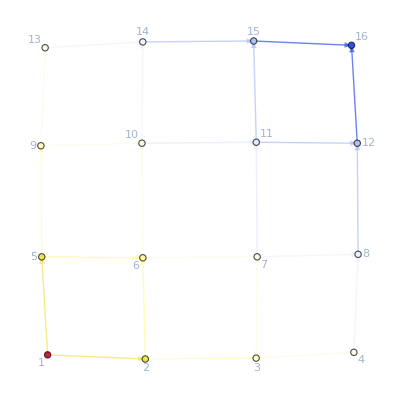

```mathematica
eme=4;
ege=4;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
systemgrid//Solve//FindInstance
```

FindInstance[{{jt28→ConditionalExpression[1/7 (6-7 jt31), 0≤jt31≤6/7],jt40→ConditionalExpression[1/7 (4-7 jt43), 0≤jt43≤4/7],jt64→ConditionalExpression[1/7 (6-7 jt67), 0≤jt67≤4/7],jt76→ConditionalExpression[1/7 (6-7 jt79), 0≤jt79≤6/7]}}]

```mathematica
Manipulate[eme=2;
ege=3;
ete =1;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0, {eme*ege*ete-1,0}, {eme*ege*ete-2,U2}},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print[timegrid];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid],{{U2,100},0,1000,10}]
```

length of system: 231

number of alernatives: 78

length of system after eliminating us: 214

new number of alernatives: 68

CCS:
j1≥0&&j2≥0&&1973600/14101+j29≥0&&1050900/14101+j30≥0&&1239200/14101+j31≥0&&734400/14101+j32≥0&&558400/14101+j33≥0&&680800/14101+j34≥0&&558400/14101+j33≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j11≥0&&j20≥0&&j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j33≥0&&-1459500/14101+j10≥0&&-19600/239+j11≥0&&-1657100/14101+j12≥0&&-853300/14101+j13≥0&&-1185600/14101+j14≥0&&-1205900/14101+j15≥0&&-436000/14101+j16≥0&&-1430400/14101+j17≥0&&-994400/14101+j18≥0&&-19600/239+j11≥0&&-2009700/14101+j20≥0&&-100+j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&jt13≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&jt19≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&jt27≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&jt33≥0&&jt34≥0&&1050900/14101+j30-jt33-jt34≥0&&jt36≥0&&jt37≥0&&j10-jt36-jt37≥0&&jt39≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&jt45≥0&&jt46≥0&&734400/14101+j32-jt45-jt46≥0&&jt48≥0&&jt49≥0&&j12-jt48-jt49≥0&&jt51≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&jt57≥0&&jt58≥0&&680800/14101+j34-jt57-jt58≥0&&jt60≥0&&jt61≥0&&j14-jt60-jt61≥0&&jt63≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&jt69≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&j11≥0&&-19600/239+j11≥0&&jt77≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&jt83≥0&&jt84≥0&&j15-jt83-jt84≥0&&jt86≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&-1205900/14101+j15-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&jt100≥0&&jt101≥0&&jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-3024500/14101+j1==0||j1==0)&&(-2615900/14101+j2==0||j2==0)&&(j29==0||1973600/14101+j29==0)&&(j30==0||1050900/14101+j30==0)&&(j31==0||1239200/14101+j31==0)&&(j32==0||734400/14101+j32==0)&&(j33==0||558400/14101+j33==0)&&(j34==0||680800/14101+j34==0)&&(j33==0||558400/14101+j33==0)&&(-1459500/14101+j10==0||j10==0)&&(-19600/239+j11==0||j11==0)&&(-1657100/14101+j12==0||j12==0)&&(-853300/14101+j13==0||j13==0)&&(-1185600/14101+j14==0||j14==0)&&(-1205900/14101+j15==0||j15==0)&&(-436000/14101+j16==0||j16==0)&&(-1430400/14101+j17==0||j17==0)&&(-994400/14101+j18==0||j18==0)&&(-19600/239+j11==0||j11==0)&&(-2009700/14101+j20==0||j20==0)&&(-100+j21==0||j21==0)&&(j23==0||j23==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j23==0||-994400/14101+j18==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt57==0||jt60==0)&&(jt58==0||jt63==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(jt83==0||jt86==0)&&(jt84==0||-1205900/14101+j15-jt86==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0)

CCS:
14101 jt84≤1205900&&jt84≥0&&((jt58==0&&14101 jt61==436000&&(jt63==0||jt63==0))||(jt63==0&&((14101 jt58==436000&&jt61==0)||(14101 jt58≤436000&&jt58≥0&&jt58+jt61==436000/14101))))&&((14101 jt34==1050900&&jt37==606200/14101)||(jt34==197600/14101&&14101 jt37==1459500)||(14101 jt34≤1050900&&14101 jt34≥197600&&jt34+jt37==1657100/14101))&&((jt46==0&&14101 jt49==1185600&&(jt51==0||jt51==0))||(jt51==0&&((14101 jt46==734400&&jt49==451200/14101)||(14101 jt46≤734400&&jt46≥0&&jt46+jt49==1185600/14101))))&&(100==100+jt101||jt101==0)

CCS:
14101 jt84≤1205900&&jt84≥0&&((jt46==0&&14101 jt49==1185600)||(14101 jt46==734400&&14101 jt49==451200)||(jt46+jt49==1185600/14101&&jt46≥0&&14101 jt46≤734400))&&((14101 jt34==1050900&&14101 jt37==606200)||(14101 jt34==197600&&14101 jt37==1459500)||(jt34+jt37==1657100/14101&&14101 jt34≥197600&&14101 jt34≤1050900))&&((jt58==0&&14101 jt61==436000)||(14101 jt58==436000&&jt61==0)||(14101 jt58≤436000&&jt58≥0&&jt58+jt61==436000/14101))

21.1794

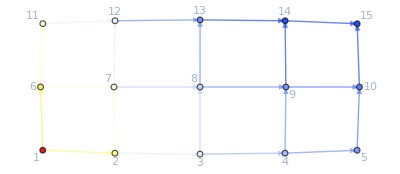

```mathematica
eme=5;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege,U1}/.U1->0, {eme*ege-1,0}, {eme*ege-2,U2}/.U2->100},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print["It took ",timegrid, " seconds to solve the critical congestion case."];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
systemgrid//Reduce[#,Reals]&
```

0≤jt61≤436000/14101&&jt58==(436000-14101 jt61)/14101&&451200/14101≤jt49≤1185600/14101&&jt46==(1185600-14101 jt49)/14101&&606200/14101≤jt37≤1459500/14101&&jt34==(1657100-14101 jt37)/14101&&0≤jt84≤1205900/14101

The error (1-Norm of LHS-RHS) is 9.9476×10^-13

The error is 9.9476×10^-13 which is less than 1.×10^-10

It took 3.79549 seconds to solve!
	The system is 200/7≤jt16≤100

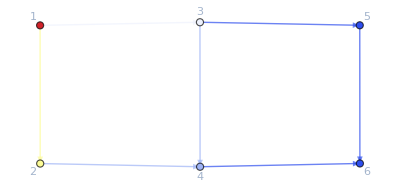

```mathematica
rulesgridsolver = Solver[d2egrid][alpha=1];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgridsolver]
```

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data]
```

```mathematica
d2egrid["EqAllAll"]
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=AbsoluteTiming@CriticalCongestionSolver[d2egrid];
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rulesgrid=KeySort@rulesgrid;
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rules0=AssociationThread[d2egrid["js"],Table[0,{i,1,Length@d2egrid["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2egrid],rules0, 1]
d2egrid["EqCriticalCase"]/.FFR
```

# TestZone

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
```

```mathematica
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
```

```mathematica
Keys[d2egrid]
```

{Vertices List,Adjacency Matrix,Entrance Vertices and Currents,Exit Vertices and Terminal Costs,Switching Costs,BG,FG,jvars,jtvars,uvars,OutRules,InRules,jays,ExitCosts,AllOr,AllEq,AllIneq,EqAllAll,BoundaryRules,Nlhs,MinimalTimeRhs,EqCriticalCase,Nrhs}

```mathematica
Length[d2egrid["AllEq"]]
Length[d2egrid["AllEq"]/.rules]
Length[d2egrid["AllOr"]]
Length[d2egrid["AllOr"]/.rules]
Length[d2egrid["AllIneq"]]
Length[d2egrid["AllIneq"]/.rules]
Length[d2egrid["EqCriticalCase"]]
Length[d2egrid["EqCriticalCase"]/.rules]
```

#### This is the winning code!

```mathematica
{system,rules}=((And@@(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["uvars"]]))//Simplify)&&system)//CleanEqualities
```

{j1≥0&&j2≥0&&1973600/14101+j29≥0&&1050900/14101+j30≥0&&1239200/14101+j31≥0&&734400/14101+j32≥0&&558400/14101+j33≥0&&680800/14101+j34≥0&&558400/14101+j33≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j11≥0&&j20≥0&&j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j33≥0&&-1459500/14101+j10≥0&&-19600/239+j11≥0&&-1657100/14101+j12≥0&&-853300/14101+j13≥0&&-1185600/14101+j14≥0&&-1205900/14101+j15≥0&&-436000/14101+j16≥0&&-1430400/14101+j17≥0&&-994400/14101+j18≥0&&-19600/239+j11≥0&&-2009700/14101+j20≥0&&-100+j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&jt13≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&jt19≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&jt27≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&jt33≥0&&jt34≥0&&1050900/14101+j30-jt33-jt34≥0&&jt36≥0&&jt37≥0&&j10-jt36-jt37≥0&&jt39≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&jt45≥0&&jt46≥0&&734400/14101+j32-jt45-jt46≥0&&jt48≥0&&jt49≥0&&j12-jt48-jt49≥0&&jt51≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&jt57≥0&&jt58≥0&&680800/14101+j34-jt57-jt58≥0&&jt60≥0&&jt61≥0&&j14-jt60-jt61≥0&&jt63≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&jt69≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&j11≥0&&-19600/239+j11≥0&&jt77≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&jt83≥0&&jt84≥0&&j15-jt83-jt84≥0&&jt86≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&-1205900/14101+j15-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&jt100≥0&&jt101≥0&&jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-3024500/14101+j1==0||j1==0)&&(-2615900/14101+j2==0||j2==0)&&(j29==0||1973600/14101+j29==0)&&(j30==0||1050900/14101+j30==0)&&(j31==0||1239200/14101+j31==0)&&(j32==0||734400/14101+j32==0)&&(j33==0||558400/14101+j33==0)&&(j34==0||680800/14101+j34==0)&&(j33==0||558400/14101+j33==0)&&(-1459500/14101+j10==0||j10==0)&&(-19600/239+j11==0||j11==0)&&(-1657100/14101+j12==0||j12==0)&&(-853300/14101+j13==0||j13==0)&&(-1185600/14101+j14==0||j14==0)&&(-1205900/14101+j15==0||j15==0)&&(-436000/14101+j16==0||j16==0)&&(-1430400/14101+j17==0||j17==0)&&(-994400/14101+j18==0||j18==0)&&(-19600/239+j11==0||j11==0)&&(-2009700/14101+j20==0||j20==0)&&(-100+j21==0||j21==0)&&(j23==0||j23==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j23==0||-994400/14101+j18==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt57==0||jt60==0)&&(jt58==0||jt63==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(jt83==0||jt86==0)&&(jt84==0||-1205900/14101+j15-jt86==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),<|j22→1805500/14101,j24→2840500/14101,u1→141500/239,u26→141500/239|>}

```mathematica
Head/@system
```

GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or

```mathematica
Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jvars"]]
```

{j1≥0&&-3024500/14101+j1≥0&&-3024500/14101+j1≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&(-3024500/14101+j1==0||j1==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),j2≥0&&-2615900/14101+j2≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&(-2615900/14101+j2==0||j2==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0),True,True,True,True,True,True,True,j10≥0&&-1459500/14101+j10≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&j10-jt36-jt37≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&(-1459500/14101+j10==0||j10==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0),j11≥0&&j11≥0&&-19600/239+j11≥0&&-19600/239+j11≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j11≥0&&-19600/239+j11≥0&&j11+j13-j20-jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&(-19600/239+j11==0||j11==0)&&(-19600/239+j11==0||j11==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0),j12≥0&&-1657100/14101+j12≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&j12-jt48-jt49≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&(-1657100/14101+j12==0||j12==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0),j13≥0&&-853300/14101+j13≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&(-853300/14101+j13==0||j13==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0),j14≥0&&-1185600/14101+j14≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&j14-jt60-jt61≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&(-1185600/14101+j14==0||j14==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0),j15≥0&&-1205900/14101+j15≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j15-jt83-jt84≥0&&-1205900/14101+j15-jt86≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&(-1205900/14101+j15==0||j15==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt84==0||-1205900/14101+j15-jt86==0),j16≥0&&-436000/14101+j16≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&(-436000/14101+j16==0||j16==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),j17≥0&&-1430400/14101+j17≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&(-1430400/14101+j17==0||j17==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),j18≥0&&-994400/14101+j18≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-994400/14101+j18==0||j18==0)&&(j23==0||-994400/14101+j18==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),True,j20≥0&&-2009700/14101+j20≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&j20-j21+jt84-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&(-2009700/14101+j20==0||j20==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0),j21≥0&&-100+j21≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&(-100+j21==0||j21==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),True,j23≥0&&j23≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&994400/14101-j18+j23≥0&&(j23==0||j23==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(j23==0||-994400/14101+j18==0),True,True,True,True,True,1973600/14101+j29≥0&&j29≥0&&j29-jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&(j29==0||1973600/14101+j29==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),1050900/14101+j30≥0&&j30≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&1050900/14101+j30-jt33-jt34≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&(j30==0||1050900/14101+j30==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),1239200/14101+j31≥0&&j31≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&(j31==0||1239200/14101+j31==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0),734400/14101+j32≥0&&j32≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&734400/14101+j32-jt45-jt46≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&(j32==0||734400/14101+j32==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0),558400/14101+j33≥0&&558400/14101+j33≥0&&j33≥0&&j33≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&(j33==0||558400/14101+j33==0)&&(j33==0||558400/14101+j33==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),680800/14101+j34≥0&&j34≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&680800/14101+j34-jt57-jt58≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&(j34==0||680800/14101+j34==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0),True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
NewReduce[And @@ (Simplify/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jtvars"]]))]
```

$Aborted

```mathematica
NewReduce[And@@(Simplify/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jtvars"]]))]
```

# This is in the code already:

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```

```mathematica
FixedPoint
```

```mathematica
system
```

j1≥0&&j2≥0&&8/7+j29≥0&&6/7+j30≥0&&4/7+j31≥0&&4/7+j32≥0&&4/7+j31≥0&&6/7+j34≥0&&8/7+j35≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j16≥0&&j23≥0&&j24≥0&&-2+j1≥0&&-2+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j31≥0&&j34≥0&&j35≥0&&-6/7+j10≥0&&-6/7+j11≥0&&-4/7+j12≥0&&-6/7+j13≥0&&-8/7+j14≥0&&-4/7+j15≥0&&-4/7+j16≥0&&-6/7+j17≥0&&-4/7+j18≥0&&-6/7+j19≥0&&-6/7+j20≥0&&-2+j21≥0&&-4/7+j16≥0&&-8/7+j23≥0&&-2+j24≥0&&-2+j1≥0&&-2+j2≥0&&2+j1-j2≥0&&2-j1+j2≥0&&-6/7+j1-j30+jt10≥0&&6/7+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-2+j1-j29+jt10≥0&&2-j1+j29+j30-jt10≥0&&jt13≥0&&8/7+j29-jt13≥0&&4/7+j29+j31-j32-jt13≥0&&-4/7-j29+j32+jt13≥0&&-4/7-j31+j32+jt13≥0&&4/7+j31-jt13≥0&&4/7+j31≥0&&j31≥0&&jt21≥0&&j2-jt21≥0&&-8/7+j2+j34-j35-jt21≥0&&8/7-j2+j35+jt21≥0&&-6/7-j34+j35+jt21≥0&&6/7+j34-jt21≥0&&jt27≥0&&jt28≥0&&6/7+j30-jt27-jt28≥0&&jt30≥0&&jt31≥0&&6/7+j34-jt30-jt31≥0&&jt33≥0&&6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33≥0&&-12/7+j11-j30-j34+jt27+jt28+jt30+jt31≥0&&j30-jt30-jt33≥0&&-6/7-j10+j11-j30+jt28+jt30+jt31+jt33≥0&&j10-jt28-jt31≥0&&jt39≥0&&jt40≥0&&4/7+j32-jt39-jt40≥0&&jt42≥0&&jt43≥0&&j10-jt42-jt43≥0&&jt45≥0&&j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45≥0&&-4/7-j10+j13-j32+jt39+jt40+jt42+jt43≥0&&j32-jt42-jt45≥0&&-6/7-j12+j13-j32+jt40+jt42+jt43+jt45≥0&&j12-jt40-jt43≥0&&jt51≥0&&4/7+j31-jt51≥0&&4/7+j12-j14+j31-jt51≥0&&-4/7+j14-j31+jt51≥0&&-4/7-j12+j14+jt51≥0&&-4/7+j12-jt51≥0&&jt57≥0&&8/7+j35-jt57≥0&&4/7+j15-j16+j35-jt57≥0&&-8/7+j16-j35+jt57≥0&&-4/7-j15+j16+jt57≥0&&j15-jt57≥0&&jt63≥0&&jt64≥0&&j11-jt63-jt64≥0&&jt66≥0&&jt67≥0&&j15-jt66-jt67≥0&&jt69≥0&&-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69≥0&&-j11-j15+j18+jt63+jt64+jt66+jt67≥0&&-6/7+j11-jt66-jt69≥0&&2/7-j11-j17+j18+jt64+jt66+jt67+jt69≥0&&j17-jt64-jt67≥0&&jt75≥0&&jt76≥0&&j13-jt75-jt76≥0&&jt78≥0&&jt79≥0&&j17-jt78-jt79≥0&&jt81≥0&&-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81≥0&&-j13-j17+j20+jt75+jt76+jt78+jt79≥0&&-6/7+j13-jt78-jt81≥0&&-j13-j19+j20+jt76+jt78+jt79+jt81≥0&&j19-jt76-jt79≥0&&jt87≥0&&j14-jt87≥0&&j14+j19-j21-jt87≥0&&-j14+j21+jt87≥0&&-8/7-j19+j21+jt87≥0&&-6/7+j19-jt87≥0&&j16≥0&&-4/7+j16≥0&&-4/7+j16-jt100≥0&&4/7-j16+j18+jt100≥0&&4/7+j18-j23+jt100≥0&&-4/7+j16-j18+j23-jt100≥0&&-8/7+j23-jt100≥0&&jt100≥0&&jt101≥0&&j20-jt101≥0&&j20+j23-j24-jt101≥0&&-j20+j24+jt101≥0&&-6/7-j23+j24+jt101≥0&&-8/7+j23-jt101≥0&&-2+j24≥0&&2+j21-j24≥0&&-2+j21≥0&&2-j21+j24≥0&&u1≥u26&&0≥-52/7+u1&&(-2+j1==0||j1==0)&&(-2+j2==0||j2==0)&&(j29==0||8/7+j29==0)&&(j30==0||6/7+j30==0)&&(j31==0||4/7+j31==0)&&(j32==0||4/7+j32==0)&&(j31==0||4/7+j31==0)&&(j34==0||6/7+j34==0)&&(j35==0||8/7+j35==0)&&(-6/7+j10==0||j10==0)&&(-6/7+j11==0||j11==0)&&(-4/7+j12==0||j12==0)&&(-6/7+j13==0||j13==0)&&(-8/7+j14==0||j14==0)&&(-4/7+j15==0||j15==0)&&(-4/7+j16==0||j16==0)&&(-6/7+j17==0||j17==0)&&(-4/7+j18==0||j18==0)&&(-6/7+j19==0||j19==0)&&(-6/7+j20==0||j20==0)&&(-2+j21==0||j21==0)&&(-4/7+j16==0||j16==0)&&(-8/7+j23==0||j23==0)&&(-2+j24==0||j24==0)&&(-2+j1==0||-2+j2==0)&&(jt10==0||2-j1+j29+j30-jt10==0)&&(jt100==0||-4/7+j16-j18+j23-jt100==0)&&(jt101==0||j20+j23-j24-jt101==0)&&(j20-jt101==0||-6/7-j23+j24+jt101==0)&&(-j20+j24+jt101==0||-8/7+j23-jt101==0)&&(-2+j24==0||-2+j21==0)&&(-2+j1-j29+jt10==0||6/7+j30-jt10==0)&&(jt13==0||4/7+j29+j31-j32-jt13==0)&&(8/7+j29-jt13==0||-4/7-j31+j32+jt13==0)&&(-4/7-j29+j32+jt13==0||4/7+j31-jt13==0)&&(4/7+j31==0||j31==0)&&(jt21==0||-8/7+j2+j34-j35-jt21==0)&&(j2-jt21==0||-6/7-j34+j35+jt21==0)&&(8/7-j2+j35+jt21==0||6/7+j34-jt21==0)&&(jt27==0||jt30==0)&&(jt28==0||jt33==0)&&(6/7+j30-jt27-jt28==0||j30-jt30-jt33==0)&&(jt31==0||6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33==0)&&(6/7+j34-jt30-jt31==0||-6/7-j10+j11-j30+jt28+jt30+jt31+jt33==0)&&(-12/7+j11-j30-j34+jt27+jt28+jt30+jt31==0||j10-jt28-jt31==0)&&(jt39==0||jt42==0)&&(jt40==0||jt45==0)&&(4/7+j32-jt39-jt40==0||j32-jt42-jt45==0)&&(jt43==0||j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45==0)&&(j10-jt42-jt43==0||-6/7-j12+j13-j32+jt40+jt42+jt43+jt45==0)&&(-4/7-j10+j13-j32+jt39+jt40+jt42+jt43==0||j12-jt40-jt43==0)&&(jt51==0||4/7+j12-j14+j31-jt51==0)&&(4/7+j31-jt51==0||-4/7-j12+j14+jt51==0)&&(-4/7+j14-j31+jt51==0||-4/7+j12-jt51==0)&&(jt57==0||4/7+j15-j16+j35-jt57==0)&&(8/7+j35-jt57==0||-4/7-j15+j16+jt57==0)&&(-8/7+j16-j35+jt57==0||j15-jt57==0)&&(jt63==0||jt66==0)&&(jt64==0||jt69==0)&&(j11-jt63-jt64==0||-6/7+j11-jt66-jt69==0)&&(jt67==0||-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69==0)&&(j15-jt66-jt67==0||2/7-j11-j17+j18+jt64+jt66+jt67+jt69==0)&&(-6/7+j1-j30+jt10==0||j29-jt10==0)&&(-j11-j15+j18+jt63+jt64+jt66+jt67==0||j17-jt64-jt67==0)&&(jt75==0||jt78==0)&&(jt76==0||jt81==0)&&(j13-jt75-jt76==0||-6/7+j13-jt78-jt81==0)&&(jt79==0||-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81==0)&&(j17-jt78-jt79==0||-j13-j19+j20+jt76+jt78+jt79+jt81==0)&&(-j13-j17+j20+jt75+jt76+jt78+jt79==0||j19-jt76-jt79==0)&&(jt87==0||j14+j19-j21-jt87==0)&&(j14-jt87==0||-8/7-j19+j21+jt87==0)&&(-j14+j21+jt87==0||-6/7+j19-jt87==0)&&(j16==0||-4/7+j16==0)&&(-4/7+j16-jt100==0||4/7+j18-j23+jt100==0)&&(4/7-j16+j18+jt100==0||-8/7+j23-jt100==0)&&(2+j1-j2==0||u1-u26==0)&&(2-j1+j2==0||u1-u26==0)&&(2+j21-j24==0||52/7-u1==0)&&(2-j21+j24==0||52/7-u1==0)

```mathematica
systemgrid
```

0≤jt79≤6/7&&jt76==1/7 (6-7 jt79)&&0≤jt67≤4/7&&jt64==1/7 (6-7 jt67)&&0≤jt43≤4/7&&jt40==1/7 (4-7 jt43)&&0≤jt31≤6/7&&jt28==1/7 (6-7 jt31)

```mathematica
FreeQ[u1][system]
And@@(FreeQ[#][system]&/@{u1,u2,u3,u4,u5})
```

False

False

```mathematica
FreeQ[#][systemgrid]&/@{u1,u2,u3,u4,u5}
```

{True,True,True,True,True}